```mathematica
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
0 | 2021-02-03 | 37266.4 | 37790. | 0.0452987 | 0.0337738
1 | 2021-02-02 | 35615.9 | 36535. | 0.059664 | 0.0641463)

```mathematica
dates=Table[DateObject[data[[k,2]]], {k,2,Length[data]}];
```

```mathematica
Length[dates]
```

678

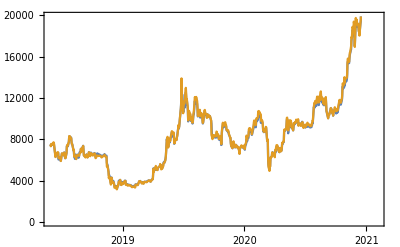

```mathematica
DateListPlot[{{dates,data[[2;;,3]]}ᵀ, {dates, data[[2;;,4]]}ᵀ}]
```

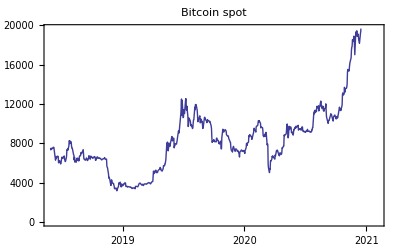

```mathematica
p1=DateListPlot[{dates,data[[2;;,3]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Bitcoin spot"]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

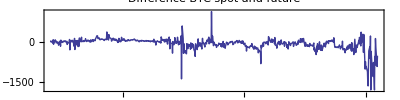

```mathematica
p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

```mathematica
r=data⟦2;;All,5⟧;
f=data⟦2;;All,6⟧;
sr=Sort[r];
m=Mean[r];
s=StandardDeviation[r];
l=Length[r];
```

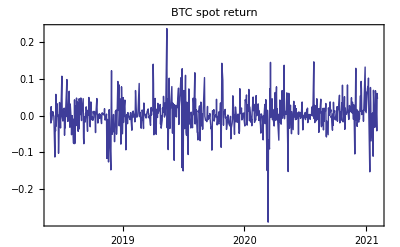

```mathematica
p3=DateListPlot[{dates,r}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_return_series.pdf", p3]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_return_series.pdf

```mathematica
extremes=Sort[Abs[r]][[-30;;]];
pos=Flatten[Table[Position[Abs[r],extremes[[k]]], {k,1,Length[extremes]}]];
```

```mathematica
p3a=DateListPlot[{dates[[pos]], r[[pos]]}ᵀ,PlotStyle->{Red,Thick},Joined->False];
```

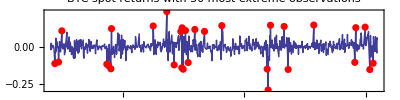

```mathematica
p3b=Show[p3,p3a, PlotLabel->"BTC spot returns with 30 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p3b]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

```mathematica
NMaximize[{LogLikelihood[StudentTDistribution[ν], (r-m)/s],ν>2}, ν]
```

{-930.714,{ν→7.94508}}

Generalized Pareto distribution

```mathematica
K=Ceiling[l 0.05];
u=-sr⟦K⟧
```

0.0652943

```mathematica
y=-sr⟦1;;K-1⟧-u;
```

```mathematica
g[x_,β_,ξ_]:=1-(1+ξ x/β)^(-1/ξ)
```

```mathematica
NMaximize[{Total[Log[g[y,β,ξ]]],ξ>0&& β>0},{β,ξ}]
```

{0.,{β→6.58869×10^-8,ξ→0.203272}}

```mathematica
1/0.203272
```

4.91952

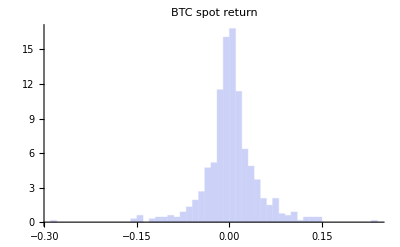

```mathematica
p4=Histogram[data[[2;;,5]],Automatic, "PDF", PlotTheme->"Classic", PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_hist.pdf", p4]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_hist.pdf

See gretl for summary statistics

```mathematica
t=Table[{InverseCDF[NormalDistribution[m,s],(k-0.5)/l],sr[[k]]}, {k,1,l}];
```

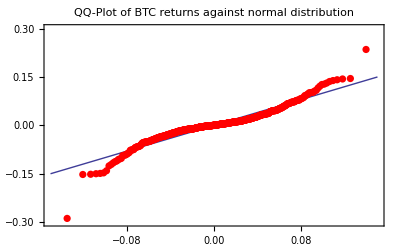

```mathematica
p5=Show[
Plot[x, {x,-0.15, 0.15},PlotTheme->"Classic",PlotRange->{-0.3,0.3}, Frame->True,PlotLabel->"QQ-Plot of BTC returns against normal distribution"],
ListPlot[t, PlotTheme->"Classic", PlotStyle->{Red, PointSize[0.013]},PlotRange->All]
]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_qq.pdf", p5]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_qq.pdf

Outliers are 3/2 times beyond the interquartile range; far outliers are beyond 3 times  the interquartile range.

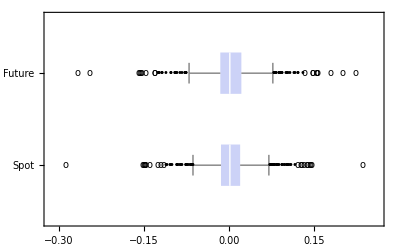

```mathematica
p6=BoxWhiskerChart[{r,f},{{"Outliers", "•"},{"FarOutliers", o}},PlotTheme->"Classic",  ChartLabels->{"Spot", "Future"},BarOrigin->Left]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_box.pdf", p6]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_box.pdf

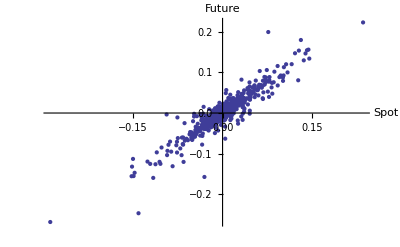

```mathematica
p7=ListPlot[{r,f}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_scatter.pdf", p7]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_scatter.pdf

## Copula scatterplots

```mathematica
sp[dist_]:=12 NIntegrate[CDF[dist,{u,v}], {u,0,1}, {v,0,1}]-3
```

Gaussian copula / Spearman’s rho

```mathematica
sol=Solve[ 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.765367}}

```mathematica
gaussian = CopulaDistribution[{"Binormal", ρ/.sol[[1]]}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gaussian]
```

0.75

```mathematica
Plot3D[PDF[gaussian, {u,v}], {u,0,1}, {v,0,1},PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
r1=RandomVariate[gaussian, 1000];
```

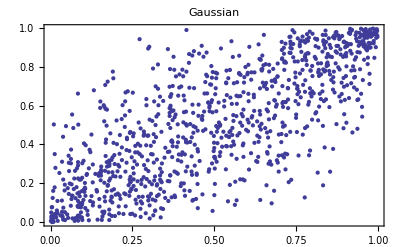

```mathematica
p1=ListPlot[r1,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Gaussian"]
```

Multivariate T

```mathematica
ρ=0.77025;StudentT=CopulaDistribution[{"MultivariateT", {{1,ρ}, {ρ,1}}, 10}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[StudentT]
```

0.749847

```mathematica
r2=RandomVariate[StudentT, 1000];
```

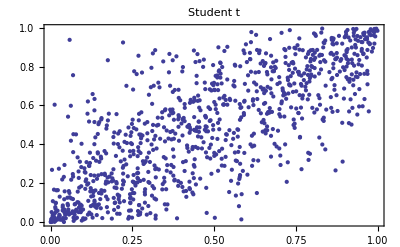

```mathematica
p2=ListPlot[r2,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Student t"]
```

Clayton

```mathematica
c=0.3875;
clayton = CopulaDistribution[{"Clayton", c}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[clayton]
```

0.75009

```mathematica
r3=RandomVariate[clayton, 1000];
```

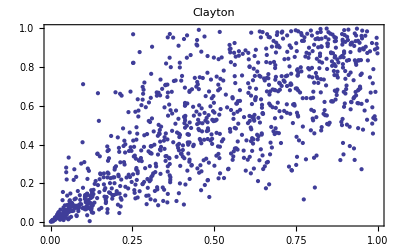

```mathematica
p3=ListPlot[r3,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Clayton"]
```

Frank

```mathematica
α=0.001199;
frank = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[frank]
```

0.750022

```mathematica
r4=RandomVariate[frank, 1000];
```

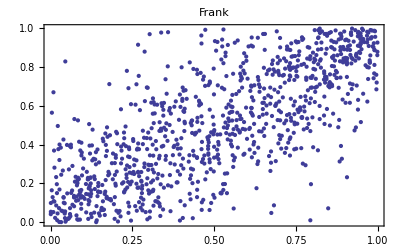

```mathematica
p4=ListPlot[r4,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Frank"]
```

Gumbel

```mathematica
α=2.2855;
gumbel=CopulaDistribution[{"GumbelHougaard", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gumbel]
```

0.750056

```mathematica
r5=RandomVariate[gumbel, 1000];
```

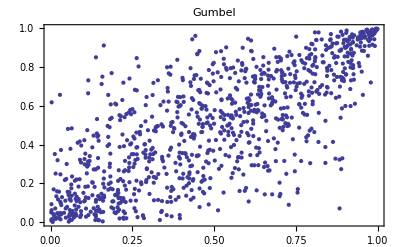

```mathematica
p5=ListPlot[r5,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Gumbel"]
```

Plackett
From Nelsen, p.99/100

From Nelsen, p. 171:

```mathematica
Clear[θ]
NSolve[0.75==(θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2,θ]
```

NSolve[0.75==(θ+1)/(θ-1)-(2 θ log(θ))/(θ-1)^2,θ]

```mathematica
sol=NMinimize[{(0.75-((θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2))^2,θ>0},{θ,15,20}]
```

{6.48932×10^-16,{θ→17.1395}}

```mathematica
θ=θ/.sol[[2]];
u=RandomVariate[UniformDistribution[],1000];
t=RandomVariate[UniformDistribution[],1000];
```

```mathematica
a=t (1-t);
b=θ+a (θ-1)^2;
c=2 a (u θ^2+1-u)+θ (1-2 a);
d=√θ √(θ+4 a u (1-u) (1-θ)^2);
v=(c-(1-2t )d)/(2 b);
```

```mathematica
r6 = {u,v}ᵀ;
```

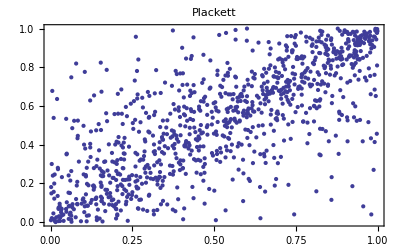

```mathematica
p6=ListPlot[r6,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Plackett"]
```

NIG factor model

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

```mathematica
α=1.5;
β=0.1;
Clear[δ]
```

Spearman Rho approximation of Gaussian

```mathematica
sol=NSolve[(6 ArcSin[δ/(2 δs[α,β])])/π==0.75, δ]
```

{{δ→1.14041}}

```mathematica
δ=δ/.sol⟦1⟧;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
Y=RandomVariate[NormalDistribution[],{3,1000}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], 1000];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], 1000];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], 1000];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
SpearmanRho[X1,X2]
```

0.734809

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Timing[
usim = hatF[X1];
vsim = hatF[X2];
]
```

{0.043189,Null}

```mathematica
r7 = {usim,vsim}ᵀ;
```

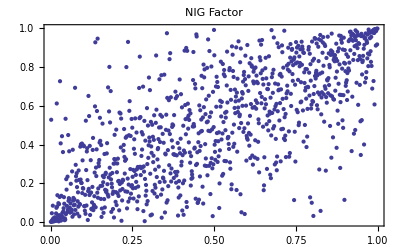

```mathematica
p7=ListPlot[r7,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"NIG Factor"]
```

Mixture copula

```mathematica
Clear[ρ,p]
```

```mathematica
p=0.8;
sol=Solve[ p 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.942793}}

```mathematica
ρ=ρ/.sol[[1]]
```

0.942793

```mathematica
mixture = p CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}] + (1-p) CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}]]
```

-8.88178×10^-16

```mathematica
p sp[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}]]
```

0.75

```mathematica
Plot3D[p PDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p) PDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}], {u,0,1}, {v,0,1}]
```

-Graphics3D-

```mathematica
X=RandomVariate[NormalDistribution[],1000];
Z=RandomVariate[NormalDistribution[],1000];
W=RandomVariate[UniformDistribution[],1000];
```

```mathematica
Y=ConstantArray[0, 1000];
```

```mathematica
Table[If[W⟦k⟧≤p,Y⟦k⟧=ρ X⟦k⟧+√(1-ρ^2) Z⟦k⟧,Y⟦k⟧=Z⟦k⟧],{k,1,1000}];
```

```mathematica
Timing[
usim = hatF[X];
vsim = hatF[Y];
]
```

{0.043284,Null}

```mathematica
r8 = {usim,vsim}ᵀ;
```

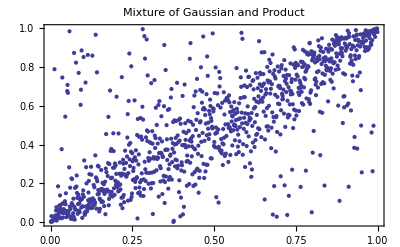

```mathematica
p8=ListPlot[r8,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Mixture of Gaussian and Product"]
```

```mathematica
p CDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p)CDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}]/.{u->.85, v->.65}
```

0.629627

```mathematica
Length[Select[{usim, vsim}ᵀ, #1[[1]]<=0.85 && #1[[2]]≤0.65&]]/1000.
```

0.633

```mathematica
Grid[{{p1, p2, p3, p4}, {},{p5, p6, p7, p8}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copulas_scatterplots.pdf", %]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copulas_scatterplots.pdf